```mathematica
RepFunc[f_,reps_]:=If[reps==0,#&,f[RepFunc[f,reps-1][#]]&];
ToPlane[cpnts_]:=cpnts/.(c_/;NumberQ[c]):>{Re[c],Im[c]};
ExpFixPoint=RepFunc[Log,200][1.1];
ExpFixPointNeg = Conjugate[ExpFixPoint];
```

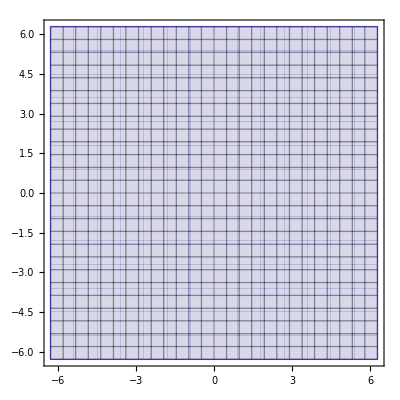

```mathematica
ParametricPlot[{x,y},{x,-2π,2π},{y,-2π,2π},Mesh->25]
```

```mathematica
ξ[z_]:=(z-ExpFixPoint)/(z-ExpFixPointNeg);
```

```mathematica
xmin=-10;xmax=10; ymin=0;ymax=2π;
Manipulate[
GraphicsRow[{
Show[
ParametricPlot[{x,y},{x,xmin,xmax},{y,ymin,ymax},Mesh->25],
ListPlot[{{pntx,pnty}}]
],
Show[
ParametricPlot[{Re[ξ[x+I y]],Im[ξ[x+I y]]},{x,xmin,xmax},{y,ymin,ymax},Mesh->100,PlotRange->Full],
ListPlot[{{Re[ξ[pntx+I pnty]],Im[ξ[pntx+I pnty]]}}]
]
}],
{pntx,xmin,xmax},{pnty,ymin,ymax}]
```

```mathematica
Manipulate[
ParametricPlot[{(1-α)x+α Re[ξ[x+I y]],(1-α) y+α Im[ξ[x+I y]]},{x,xmin,xmax},{y,ymin,ymax},PlotRange->Full],
{α,0,1}]
```